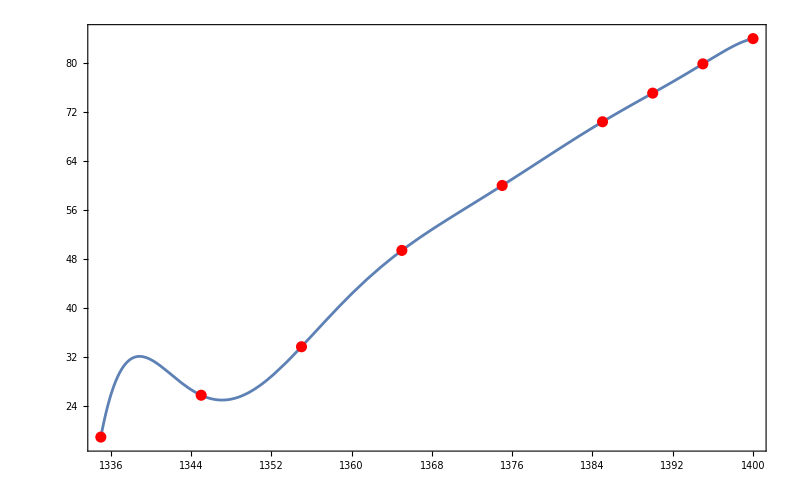

```mathematica
xj={1335,1345,1355,1365,1375,1385,1390,1395,1400};
fj={18.95,25.79,33.71,49.45,60.06,70.47,75.15,79.93,84.06};
a=Min[xj];
b=Max[xj];
n=Length[xj];
L[j_Integer,x_]:=(∏_(k=1)^(j-1) (x-xj[[k]])/(xj[[j]]-xj[[k]])) (∏_(k=j+1)^n (x-xj[[k]])/(xj[[j]]-xj[[k]]));
p[x_]:=∑_(j=1)^n fj[[j]] L[j,x];
p1=Plot[p[x],{x,a,b},DisplayFunction->Identity];
p2=ListPlot[Table[{xj[[j]],fj[[j]]},{j,1,n}],PlotStyle->{RGBColor[1,0,0],PointSize[0.01]},DisplayFunction->Identity];
Show[p1,p2,DisplayFunction->$DisplayFunction,Frame->True,PlotRange->{18,85},Axes->False]
```

```mathematica
p[1330]
p[1340]
p[1359]
p[1367]
p[1405]
```

-100.318

31.5909

40.715

51.7807

76.1744